## Cosine orthogonality

```mathematica
Clear[m]
```

Constant

```mathematica
Integrate[Cos[30π y/L]C1,{y,-L,L}];
```

Cosine squared

```mathematica
Integrate[Cos [3 π y/L]Cos [1 π y/L],{y,-L,L}];
```

Half space sine/cosine

```mathematica
Integrate[Cos [3 π y/L]Sin [1 π y/(2 L)],{y,-L,0}]+Integrate[Cos [3 π y/L]Sin [1 π y/(2 L)],{y,0,L}];
```

Cosine cubed

```mathematica
Integrate[Cos [0π y/L]Cos [0 π y/L]Cos [1 π y/L],{y,-L,L}];
```

third order mixed

```mathematica
Integrate[Cos [3π y/L]Cos [1 π y/L]Sin[1 π y/(2L)],{y,-L,0}]+Integrate[Cos [3π y/L]Cos [1 π y/L]Sin[1 π y/(2L)],{y,0,L}];
```

```mathematica
Integrate[Cos [2π y/L]Sin [2 π/2 y/L]Sin[1 π y/(2L)],{y,-L,0}]-Integrate[Cos [2π y/L]Sin [2 π y/(2L)]Sin[1 π y/(2L)],{y,0,L}]
```

```mathematica
Integrate[Cos [3π y/L]Sin [1 π y/(2L)]Cos[4 π y/L],{y,-L,0}]+Integrate[Cos [3π y/L]Sin [1 π y/(2L)]Cos[4 π y/L],{y,0,L}]
```

0

## Sine orthogonality

```mathematica
Integrate[Sin[0π y/(2L)]C1,{y,-L,L}];
```

```mathematica
Integrate[Sin [0 π y/(2L)]Cos [3 π y/L],{y,-L,L}]
```

0

```mathematica
Integrate[Sin [6π y/(2L)]Sin [4 π y/L],{y,-L,0}] -Integrate[Sin [6π y/(2L)]Sin [4 π y/L],{y,0,L}]
```

```mathematica
|
```

```mathematica
Integrate[Cos [3π y/L]Sin [3 π y/(2L)]Cos[1 π y/L],{y,-L,L}]
```

0

```mathematica
Integrate[Sin [3π y/(2L)]Sin [3π y/(2L)]Cos[ π y/L],{y,-L,0}]-Integrate[Sin [3π y/(2L)]Sin [3 π y/(2L)]Cos[ π y/L],{y,0,L}];
```

```mathematica
Integrate[Sin [6π y/(2L)]Sin [4π y/(2L)]Cos[ π y/L],{y,-L,L}]
```

L/2

```mathematica
Integrate[Sin [3π y/(2L)]Sin [5π y/(2L)]Sin[ π y/(2L)],{y,-L,0}]
```

(20 L)/(63 π)

```mathematica
Integrate[Sin [3π y/(2L)]Sin [5π y/(2L)]Sin[ π y/(2L)],{y,0,L}]
```

-(20 L)/(63 π)

0

```mathematica
Integrate[Cos[3π y/L]Sin [π y/(2L)]Cos[ 2π y/(2L)],{y,-L,0}]
```

(26 L)/(315 π)

```mathematica
Integrate[Cos[3π y/L]Sin [π y/(2L)]Cos[ 2π y/(2L)],{y,0,L}]
```

-(26 L)/(315 π)

## Alpha integrals

α_0

```mathematica
Integrate[Sin [n π y/(2L)]Cos [m π y/L],{y,-L,0}]
```

(2 L (n-n Cos[m π] Cos[(n π)/2]-2 m Sin[m π] Sin[(n π)/2]))/((4 m^2-n^2) π)

```mathematica
α0[m_, n_]:=If[m==2n, 0,(2 L (n-n Cos[m π] Cos[(n π)/2]))/((4 m^2-n^2) π)]
```

```mathematica
A0test = Table[α4[m,n]-Integrate[Sin [n π y/(2L)]Cos [m π y/L],{y,-L,0}],{m,0,4},{n,1,4}];
```

```mathematica
MatrixForm[A4test]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
TeXForm[(2 L (n-n Cos[m π] Cos[(n π)/2]))/((4 m^2-n^2) π)]
```

\frac{2 L \left(n-n \cos (\pi  m) \cos \left(\frac{\pi  n}{2}\right)\right)}{\pi 
   \left(4 m^2-n^2\right)}

α4

```mathematica
Integrate[Sin [n π y/(2L)]Sin [n π y/(2L)],{y,-L,0}]
```

1/2 (L-(L Sin[n π])/(n π))

```mathematica
α4[m_, n_]:=If[m!= n, ((L Sin[1/2 (m-n) π])/(m-n)-(L Sin[1/2 (m+n) π])/(m+n))/π,L/2]
```

```mathematica
A4test = Table[α4[m,n]-Integrate[Sin [n π y/(2L)]Sin [m π y/(2L)],{y,-L,0}],{m,0,4},{n,1,4}];
```

```mathematica
MatrixForm[A4test];
```

α1

```mathematica
Integrate[Sin [n π y/(2L)]Cos [m π y/L]Cos[π y/L],{y,-L,0}]
```

-(2 L (n (-4-4 m^2+n^2) (1+Cos[m π] Cos[(n π)/2])+2 m (4-4 m^2+n^2) Sin[m π] Sin[(n π)/2]))/((16 m^4+(-4+n^2)^2-8 m^2 (4+n^2)) π)

```mathematica
α1[m_, n_]:= If[n ==2(m -1),0, If[n== 2(m +1),0, If[n==-2(m+1), 0, If[n == -2(m-1),0,-(2 L (n (-4-4 m^2+n^2) (1+Cos[m π] Cos[(n π)/2])))/((16 m^4+(-4+n^2)^2-8 m^2 (4+n^2)) π)]]]]
```

```mathematica
A1test = Table[α1[m,n]-Integrate[Sin [n π y/(2L)]Cos [m π y/L]Cos[π y/L],{y,-L,0}],{m,0,4},{n,1,4}];
```

```mathematica
MatrixForm[A1test]
```

```mathematica
TeXForm[-(2 L (n (-4-4 m^2+n^2) (1+Cos[m π] Cos[(n π)/2])))/((16 m^4+(-4+n^2)^2-8 m^2 (4+n^2)) π)]
```

-\frac{2 L n \left(-4 m^2+n^2-4\right) \left(\cos (\pi  m) \cos \left(\frac{\pi 
   n}{2}\right)+1\right)}{\pi  \left(16 m^4-8 m^2
   \left(n^2+4\right)+\left(n^2-4\right)^2\right)}

α2

```mathematica
α2[m_, n_]:= If[m==0 && n==1, L/2,If[n ==2m -1, -L/4, If[n== 2m +1, L/4, If[n==-1-2m, -L/4, If[n ==1-2m, L/4, (L ((2 (2 m-n) Cos[m π-(n π)/2])/(-1+(-2 m+n)^2)-(2 (2 m+n) Cos[m π+(n π)/2])/(-1+4 m^2+4 m n+n^2)))/(2 π)]]]]]
```

```mathematica
A2test = Table[α2[m,n]-Integrate[Sin [n π y/(2L)]Cos [m π y/L]Sin[π y/(2L)],{y,-L,0}],{m,0,10},{n,1,10}];
```

```mathematica
MatrixForm[A2test]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Integrate[Sin [1 π y/(2L)]Cos [0 π y/L]Sin[π y/(2L)],{y,-L,0}]
```

L/2

```mathematica
Solve[-1+(-2 m+n)^2==0,n]
```

{{n→-1+2 m},{n→1+2 m}}

```mathematica
Solve[-1+4 m^2+4 m n+n^2==0, n]
```

{{n→-1-2 m},{n→1-2 m}}

```mathematica
Integrate[Sin [(2*0+1) π y/(2L)]Cos [0 π y/L]Sin[π y/(2L)],{y,-L,0}]
```

L/2

α3

```mathematica
Integrate[Cos[m π/L y]Sin[π y/(2L)] Cos[n π/L y],{y,0,-L}]
```

(2 L (1-4 m^2-4 n^2+2 m (-1+4 m^2-4 n^2) Cos[n π] Sin[m π]+2 n (-1-4 m^2+4 n^2) Cos[m π] Sin[n π]))/((16 m^4+(1-4 n^2)^2-8 m^2 (1+4 n^2)) π)

```mathematica
Solve[(16 m^4+(1-4 n^2)^2-8 m^2 (1+4 n^2)) π==0, n]
```

{{n→1/2 (-1-2 m)},{n→1/2 (1-2 m)},{n→1/2 (-1+2 m)},{n→1/2 (1+2 m)}}

```mathematica
α3[n_, m_]:=If[n==1/2(1-2m), 0, If[ n== 1/2(-1-2m), 0, If[n==1/2(1+2m),0,If[n==1/2(-1+2m),0,  (2 L (1-4 m^2-4 n^2))/((16 m^4+(1-4 n^2)^2-8 m^2 (1+4 n^2)) π)]]]]
```

```mathematica
A3test = Table[α3[m,n]-Integrate[Cos[m π/L y]Sin[π y/(2L)] Cos[n π/L y],{y,0,-L}],{m,0,10},{n,1,10}];
```

```mathematica
MatrixForm[A3test]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
TeXForm[  (2 L (1-4 m^2-4 n^2))/((16 m^4+(1-4 n^2)^2-8 m^2 (1+4 n^2)) π)]
```

\frac{2 L \left(-4 m^2-4 n^2+1\right)}{\pi  \left(16 m^4-8 m^2 \left(4
   n^2+1\right)+\left(1-4 n^2\right)^2\right)}

α5

```mathematica
Integrate[Sin[m π/(2L)y]Cos[π y/L] Sin[(0) π/(2L)y],{y,-L,0}]
```

0

```mathematica
α5[m_, n_]:= If [m n ==0, 0, If[n==m-2, L/4, If[n==m+2, L/4,If[n==-2-m, -L/4, If[n==2-m, -L/4,(L (((-m+n) Sin[1/2 (m-n) π])/(-4+(m-n)^2)+((m+n) Sin[1/2 (m+n) π])/((-2+m+n) (2+m+n))))/π ]] ]]]
```

```mathematica
A5test = Table[α5[m,n]-Integrate[Sin[m π/(2L)y]Sin[π n y/(2L)] Cos[ π/L y],{y,-L,0}],{m,0,5},{n,0,5}];
```

```mathematica
MatrixForm[A5test]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Solve[(-2+m+n) (2+m+n)==0, n]
```

{{n→-2-m},{n→2-m}}

```mathematica
Solve[-4+(m-n)^2==0, n]
```

{{n→-2+m},{n→2+m}}

```mathematica
TeXForm[(L (((-m+n) Sin[1/2 (m-n) π])/(-4+(m-n)^2)+((m+n) Sin[1/2 (m+n) π])/((-2+m+n) (2+m+n))))/π]
```

\frac{L \left(\frac{(n-m) \sin \left(\frac{1}{2} \pi 
   (m-n)\right)}{(m-n)^2-4}+\frac{(m+n) \sin \left(\frac{1}{2} \pi 
   (m+n)\right)}{(m+n-2) (m+n+2)}\right)}{\pi }

```mathematica
Sinh[0]
```

0

```mathematica
Integrate[Cos[1 π y/L],{y,-L, L}]
```

0

```mathematica
Sum[(-1)^n/n, {n,1, Infinity}]
```

-Log[2]

```mathematica
(-1))^n
```

-1

```mathematica
Integrate[Cos[n π/L y]Cos[m π/L y]/.{m->0, n->0},{y,-L,L}]
```

2 L

```mathematica
Integrate[Sin[n π/(2L)y],{y,-L,0}]
```

-(4 L Sin[(n π)/4]^2)/(n π)

```mathematica
Integrate[Cos[n π/L y]Sin[m π/(2L)y],{y,-L,0}]
```

```mathematica
(2 L (-m+m Cos[(m π)/2] Cos[n π]))/((m^2-4 n^2) π)
```

(2 L (-m+m Cos[(m π)/2] Cos[n π]))/((m^2-4 n^2) π)

```mathematica
Sum[(-1)^n/n,{n,1,∞}]
```

-Log[2]

```mathematica
Sinh[x]
```

Sinh[x]

```mathematica
Simplify[TrigToExp[Sinh[x]]]
```

1/2 ⅇ^-x (-1+ⅇ^(2 x))

```mathematica
Solve[A Sinh[x]==0, A]
```

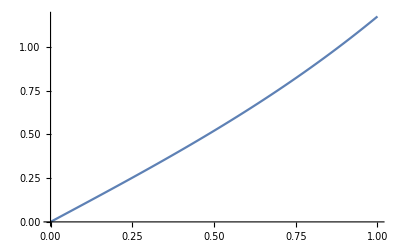

```mathematica
Plot[c Sinh[x],{x,0,1}]
```

```mathematica
Cosh[0]
```

1

```mathematica
Integrate[Cos[3 π/L y]Cos[0 π/L y],{y,-L,L}]
```

0

```mathematica
(2 L Sin[n π])/(n π)/.n->0
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0 L ComplexInfinity)/π encountered.

Indeterminate

```mathematica
Sin[A+ B]
```

Sin[A+B]

```mathematica
TrigExpand[Sin[A+B]]
```

Cos[B] Sin[A]+Cos[A] Sin[B]

```mathematica
Cos[A+B]
```

Cos[A+B]

```mathematica
C
```

C

```mathematica
TrigExpand[Cos[A+B+CC+ DD + EE + FF]]/.Cos[A]->0
```

-Cos[CC] Cos[DD] Cos[EE] Cos[FF] Sin[A] Sin[B]-Cos[B] Cos[DD] Cos[EE] Cos[FF] Sin[A] Sin[CC]-Cos[B] Cos[CC] Cos[EE] Cos[FF] Sin[A] Sin[DD]+Cos[EE] Cos[FF] Sin[A] Sin[B] Sin[CC] Sin[DD]-Cos[B] Cos[CC] Cos[DD] Cos[FF] Sin[A] Sin[EE]+Cos[DD] Cos[FF] Sin[A] Sin[B] Sin[CC] Sin[EE]+Cos[CC] Cos[FF] Sin[A] Sin[B] Sin[DD] Sin[EE]+Cos[B] Cos[FF] Sin[A] Sin[CC] Sin[DD] Sin[EE]-Cos[B] Cos[CC] Cos[DD] Cos[EE] Sin[A] Sin[FF]+Cos[DD] Cos[EE] Sin[A] Sin[B] Sin[CC] Sin[FF]+Cos[CC] Cos[EE] Sin[A] Sin[B] Sin[DD] Sin[FF]+Cos[B] Cos[EE] Sin[A] Sin[CC] Sin[DD] Sin[FF]+Cos[CC] Cos[DD] Sin[A] Sin[B] Sin[EE] Sin[FF]+Cos[B] Cos[DD] Sin[A] Sin[CC] Sin[EE] Sin[FF]+Cos[B] Cos[CC] Sin[A] Sin[DD] Sin[EE] Sin[FF]-Sin[A] Sin[B] Sin[CC] Sin[DD] Sin[EE] Sin[FF]

```mathematica
TrigExpand[Cos[n π 1/2 + ϵ  + ϵ^2+ϵ^3  ]]
```

Cos[(n π)/2] Cos[ϵ] Cos[ϵ^2] Cos[ϵ^3]-Cos[ϵ^2] Cos[ϵ^3] Sin[(n π)/2] Sin[ϵ]-Cos[ϵ] Cos[ϵ^3] Sin[(n π)/2] Sin[ϵ^2]-Cos[(n π)/2] Cos[ϵ^3] Sin[ϵ] Sin[ϵ^2]-Cos[ϵ] Cos[ϵ^2] Sin[(n π)/2] Sin[ϵ^3]-Cos[(n π)/2] Cos[ϵ^2] Sin[ϵ] Sin[ϵ^3]-Cos[(n π)/2] Cos[ϵ] Sin[ϵ^2] Sin[ϵ^3]+Sin[(n π)/2] Sin[ϵ] Sin[ϵ^2] Sin[ϵ^3]

```mathematica
Series[%72,{ϵ,0,2}]
```

Cos[(n π)/2]-Sin[(n π)/2] ϵ+(-1/2 Cos[(n π)/2]-Sin[(n π)/2]) ϵ^2+O[ϵ]^3

```mathematica
TrigExpand[Sin[n π  +  ϵ +  ϵ^2+  ϵ^3]]/. Sin[n π]->0
```

Cos[n π] Cos[ϵ^2] Cos[ϵ^3] Sin[ϵ]+Cos[n π] Cos[ϵ] Cos[ϵ^3] Sin[ϵ^2]+Cos[n π] Cos[ϵ] Cos[ϵ^2] Sin[ϵ^3]-Cos[n π] Sin[ϵ] Sin[ϵ^2] Sin[ϵ^3]

```mathematica
Series[%69, {ϵ,0,1}]
```

Cos[n π] ϵ+O[ϵ]^2

```mathematica
Cos[3 π/2]
```

0

```mathematica
Series[Cos[n π y/L + ϵ/L y+ ϵ^2/L y + ϵ^3/L y + ϵ^4/L y],{ϵ,0, 2}]
```

Cos[(n π y)/L]-(y Sin[(n π y)/L] ϵ)/L+(-(y^2 Cos[(n π y)/L])/(2 L^2)-(y Sin[(n π y)/L])/L) ϵ^2+O[ϵ]^3

```mathematica
Series[Sin[n π y/(2L) + ϵ/L y+ ϵ^2/L y + ϵ^3/L y + ϵ^4/L y],{ϵ,0, 2}]
```

Sin[(n π y)/(2 L)]+(y Cos[(n π y)/(2 L)] ϵ)/L+((y Cos[(n π y)/(2 L)])/L-(y^2 Sin[(n π y)/(2 L)])/(2 L^2)) ϵ^2+O[ϵ]^3